```mathematica
SetDirectory@NotebookDirectory[];
Quiet@Remove["Global`*"];
Needs["ErrorBarPlots`"];
```

```mathematica
GeoGraphics[GeoMarker[{{44.018089,-73.168445},{43.862657,-72.766778}}]]
```

-Graphics-

```mathematica
DateandTime = Table[DateObject[{2019,1,20,i}],{i,00,48}];
(*DateandTime = Table[DateObject[{2019,1,20,i}],{i,12,18,03}];*)
```

### Snow Accumulation Data

#### Middlebury

```mathematica
Morrison2momentaccummidd=Partition[Flatten[Import["midd_accum_data.txt", "CSV"]],49];
meanM2Mmidd=Mean[Morrison2momentaccummidd];(* Data is output as mm, but we can simply convert to cm, since we must multiply each datapoint by 10 because we assume a 10:1 snow liquid ratio. So our data work as cm. *)
M2Maccumsnowtimes=Transpose[{DateandTime,meanM2Mmidd}];
Thompsonaccummidd=Partition[Flatten[Import["midd_accum_dataTHOM.txt", "CSV"]],49];
meanTHOMmidd=Mean[Thompsonaccummidd];
Thomaccumsnowtimes = Transpose[{DateandTime, meanTHOMmidd}];
WDM6accummidd=Partition[Flatten[Import["midd_accum_dataWDM6.txt", "CSV"]],49];
meanWDM6midd=Mean[WDM6accummidd];
WDM6accumsnowtimes = Transpose[{DateandTime, meanWDM6midd}];
Millbrandtaccummidd=Partition[Flatten[Import["midd_accum_dataMillbrandt.txt", "CSV"]],49];
meanmillbrandtmidd=Mean[Millbrandtaccummidd];
Millbrandtaccumsnowtimes = Transpose[{DateandTime, meanmillbrandtmidd}];
Goddardaccummidd=Partition[Flatten[Import["midd_accum_dataGoddard.txt", "CSV"]],49];
meangoddmidd=Mean[Goddardaccummidd];
Goddardaccumsnowtimes = Transpose[{DateandTime, meangoddmidd}];
```

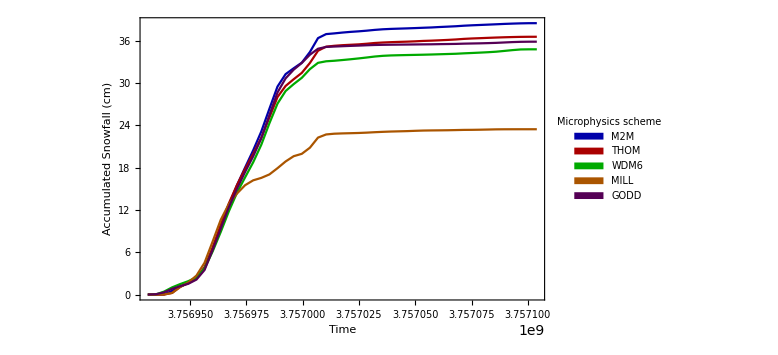

```mathematica
Accumsnowplot=DateListPlot[{meanM2Mmidd,meanTHOMmidd,meanWDM6midd, meanmillbrandtmidd,meangoddmidd},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

#### Now this includes Convective precip “SNOWC”

```mathematica
Morrison2momentaccummidd=Partition[Flatten[Import["midd_accum_dataM2Mc.txt", "CSV"]],49];
meanM2Mmidd=Mean[Morrison2momentaccummidd];(* Data is output as mm, but we can simply convert to cm, since we must multiply each datapoint by 10 because we assume a 10:1 snow liquid ratio. So our data work as cm. *)
M2Maccumsnowtimes=Transpose[{DateandTime,meanM2Mmidd}];
Thompsonaccummidd=Partition[Flatten[Import["midd_accum_dataTHOMc.txt", "CSV"]],49];
meanTHOMmidd=Mean[Thompsonaccummidd];
Thomaccumsnowtimes = Transpose[{DateandTime, meanTHOMmidd}];
WDM6accummidd=Partition[Flatten[Import["midd_accum_dataWDM6c.txt", "CSV"]],49];
meanWDM6midd=Mean[WDM6accummidd];
WDM6accumsnowtimes = Transpose[{DateandTime, meanWDM6midd}];
Millbrandtaccummidd=Partition[Flatten[Import["midd_accum_dataMILLc.txt", "CSV"]],49];
meanmillbrandtmidd=Mean[Millbrandtaccummidd];
Millbrandtaccumsnowtimes = Transpose[{DateandTime, meanmillbrandtmidd}];
```

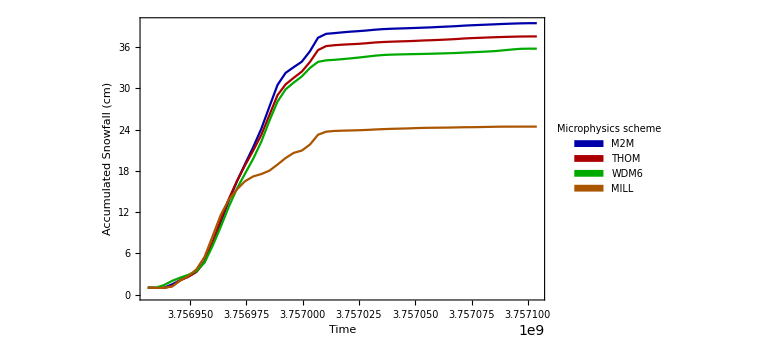

```mathematica
AccumsnowplotC=DateListPlot[{meanM2Mmidd,meanTHOMmidd,meanWDM6midd, meanmillbrandtmidd},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

```mathematica
(*Makes sense it looks exactly the same as the previous graph since I did not use a convective parameterization in my simulations*)
```

#### Rochester

```mathematica
Morrison2momentaccumroch=Partition[Flatten[Import["roch_accum_dataM2M.txt", "CSV"]],49];
meanM2Mroch=Mean[Morrison2momentaccumroch];(* Data is output as mm, but we can simply convert to cm, since we must multiply each datapoint by 10 because we assume a 10:1 snow liquid ratio. So our data work as cm. *)
M2Maccumsnowtimes=Transpose[{DateandTime,meanM2Mroch}];
```

```mathematica
Thompsonaccumroch=Partition[Flatten[Import["roch_accum_dataTHOM.txt", "CSV"]],49];
meanTHOMroch=Mean[Thompsonaccumroch];
Thomaccumsnowtimes = Transpose[{DateandTime, meanTHOMroch}];
```

```mathematica
WDM6accumroch=Partition[Flatten[Import["roch_accum_dataWDM6.txt", "CSV"]],49];
meanWDM6roch=Mean[WDM6accumroch];
WDM6accumsnowtimes = Transpose[{DateandTime, meanWDM6roch}];
```

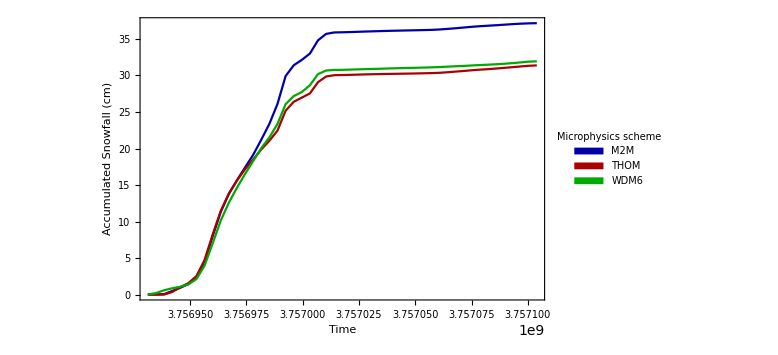

```mathematica
Accumsnowplot=DateListPlot[{meanM2Mroch,meanTHOMroch,meanWDM6roch},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Accumulated Snowfall (cm)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

### Snow Water Equivalent

```mathematica
Morrison2momentSWEmidd=Partition[Flatten[Import["midd_SWE_dataM2M.txt", "CSV"]],49];
meanM2Mmidd=Mean[Morrison2momentSWEmidd];(* Units here are kg m^-2*)
M2MSWEsnowtimes=Transpose[{DateandTime,meanM2Mmidd}];
```

```mathematica
ThompsonSWEmidd=Partition[Flatten[Import["midd_SWE_dataTHOM.txt", "CSV"]],49];
meanTHOMmidd=Mean[ThompsonSWEmidd];
ThomSWEsnowtimes = Transpose[{DateandTime, meanTHOMmidd}];
```

```mathematica
WDM6SWEmidd=Partition[Flatten[Import["midd_SWE_dataWDM6.txt", "CSV"]],49];
meanWDM6midd=Mean[WDM6SWEmidd];
WDM6SWEsnowtimes = Transpose[{DateandTime, meanWDM6midd}];
```

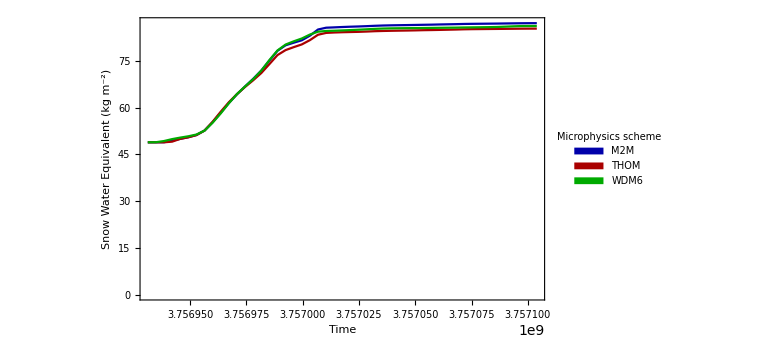

```mathematica
SWEsnowplot=DateListPlot[{meanM2Mmidd,meanTHOMmidd,meanWDM6midd},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Snow Water Equivalent (kg m^-2)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```

## All hydrometeor data mixing ratios

```mathematica
(*Note: mixing ratio is defined as g of X per kg of air*)
```

```mathematica
(*As I have it now, I can only get data for one time efficiently in NCL. I need to figure out an effective way to loop through many times to get data for snow mixing ratio. Right now I only have 14:00 UTC *)
```

```mathematica
THOMhydromidd = Partition[Partition[Flatten[Import["midd_hydrometeor_dataTHOM.txt","CSV"]],2],38];
WDM6hydromidd=Partition[Partition[Flatten[Import["midd_hydrometeor_dataWDM6.txt","CSV"]],2],38];
M2Mhydromidd = Partition[Partition[Flatten[Import["midd_hydrometeor_dataM2M.txt","CSV"]],2],38];
```

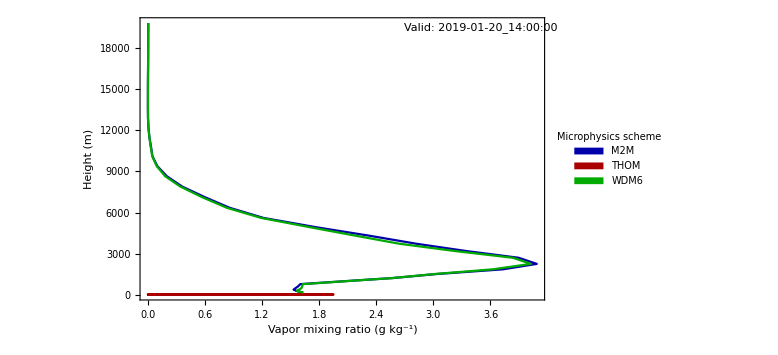

```mathematica
vaporplotmidd=ListPlot[{M2Mhydromidd⟦1⟧,THOMhydromidd⟦1⟧,WDM6hydromidd⟦1⟧},Frame->True,FrameLabel->{"Vapor mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{3.5,19500}]]
```

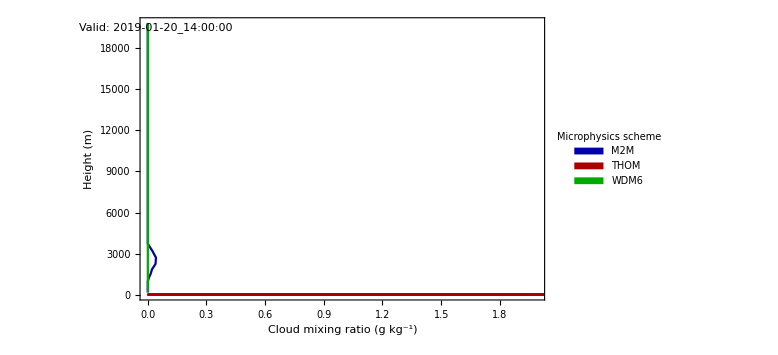

```mathematica
cloudplotmidd=ListPlot[{M2Mhydromidd⟦2⟧,THOMhydromidd⟦2⟧,WDM6hydromidd⟦2⟧},Frame->True,FrameLabel->{"Cloud mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.04,19500}]]
```

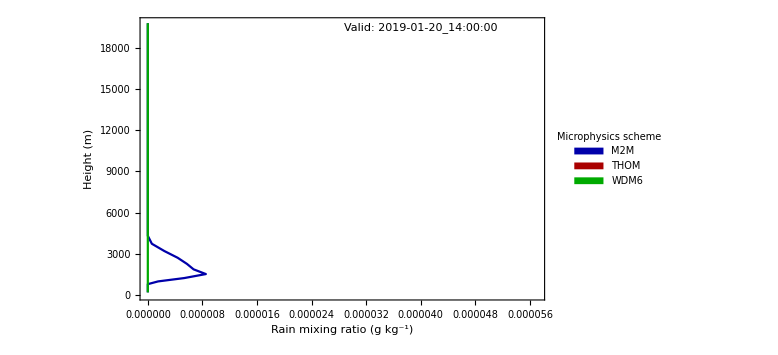

```mathematica
rainplotmidd=ListPlot[{M2Mhydromidd⟦3⟧,THOMhydromidd⟦3⟧,WDM6hydromidd⟦3⟧},Frame->True,FrameLabel->{"Rain mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,.000057},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.00004,19500}]]
```

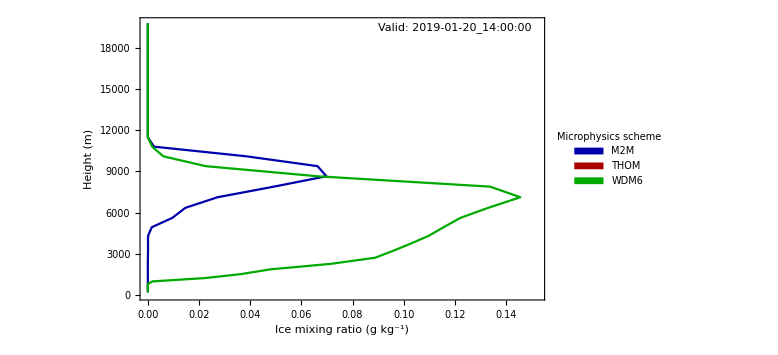

```mathematica
iceplotmidd=ListPlot[{M2Mhydromidd⟦4⟧,THOMhydromidd⟦4⟧,WDM6hydromidd⟦4⟧},Frame->True,FrameLabel->{"Ice mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{0,.152},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"],Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.12,19500}]]
```

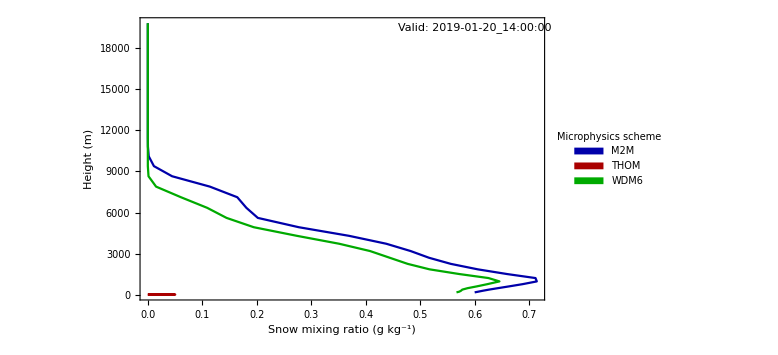

```mathematica
snowplotmidd=ListPlot[{M2Mhydromidd⟦6⟧,THOMhydromidd⟦6⟧,WDM6hydromidd⟦6⟧},Frame->True,FrameLabel->{"Snow mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.6,19500}]]
```

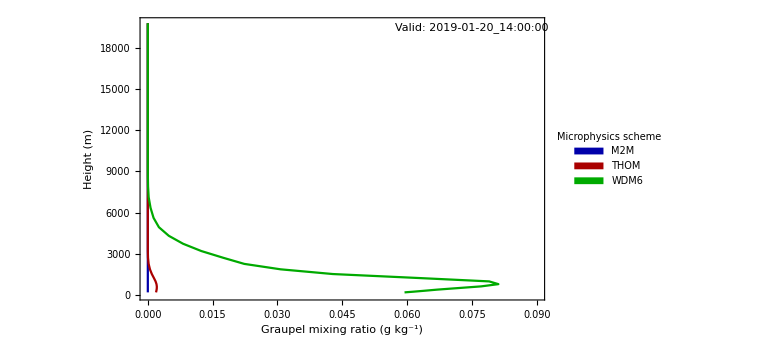

```mathematica
graupelplotmidd=ListPlot[{M2Mhydromidd⟦5⟧,THOMhydromidd⟦5⟧,WDM6hydromidd⟦5⟧},Frame->True,FrameLabel->{"Graupel mixing ratio (g kg^-1)", "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,.09},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset["Valid: 2019-01-20_14:00:00",{0.075,19500}]]
```

```mathematica
GraphicsGrid[{{vaporplotmidd,cloudplotmidd},{rainplotmidd,iceplotmidd},{snowplotmidd, graupelplotmidd}}]
```

-Graphics-

```mathematica
listTypes ={"Vapor mixing ratio (g kg^-1)","Cloud mixing ratio (g kg^-1)","Rain mixing ratio (g kg^-1)","Ice mixing ratio (g kg^-1)","Graupel mixing ratio (g kg^-1)","Snow mixing ratio (g kg^-1)"};
listTimes={"Valid: 2019-01-20_04:00:00","Valid: 2019-01-20_08:00:00","Valid: 2019-01-20_12:00:00","Valid: 2019-01-20_16:00:00","Valid: 2019-01-20_20:00:00"};
```

```mathematica
seperatetimesTHOM=Partition[Flatten[Import["midd_hydrometeor_dataTHOM.txt","CSV"]],228];
hydrometeorTHOM=Table[Partition[seperatetimesTHOM⟦i⟧,38],{i,1,6}];
listDataTHOM=Table[Table[Transpose[{hydrometeorTHOM⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,6}];
```

Transpose::nmtx: The first two levels of {{0.921394,0.890352,0.862273,0.827567,0.800027,0.831168,1.02735,1.3316,1.51267,1.52744,1.54023,1.61606,1.66366,1.67564,1.66017,1.48785,«6»,0.0785859,0.0407861,0.0232899,0.0156497,0.0134012,0.00862525,0.001,0.001,0.001,0.001,0.00242115,0.00273953,0.00305528,0.00343078,0.00389611,0.0044196},heights} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},heights} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
seperatetimesWDM6=Partition[Flatten[Import["midd_hydrometeor_dataWDM6times.txt","CSV"]],228];
hydrometeorWDM6=Table[Partition[seperatetimesWDM6⟦i⟧,38],{i,1,6}];
listDataWDM6=Table[Table[Transpose[{hydrometeorWDM6⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,6}];
```

```mathematica
seperatetimesM2M=Partition[Flatten[Import["midd_hydrometeor_dataM2Mtimes.txt","CSV"]],228];
hydrometeorM2M=Table[Partition[seperatetimesM2M⟦i⟧,38],{i,1,6}];
listDataM2M=Table[Table[Transpose[{hydrometeorM2M⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,6}];
```

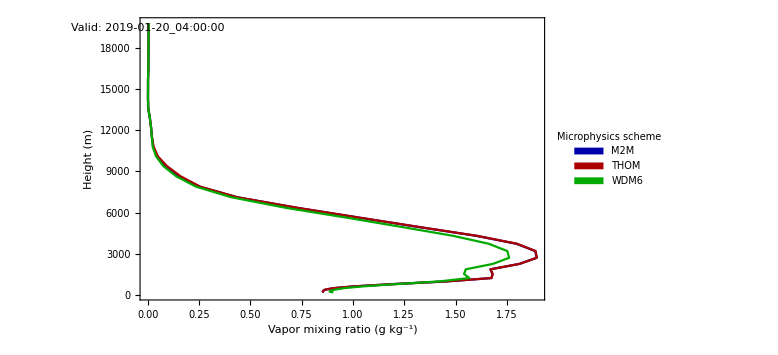

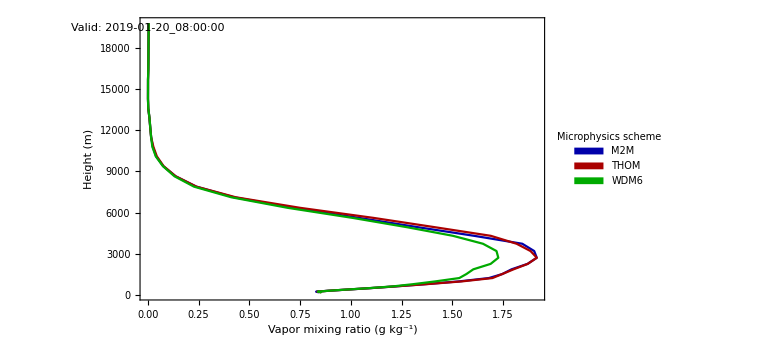

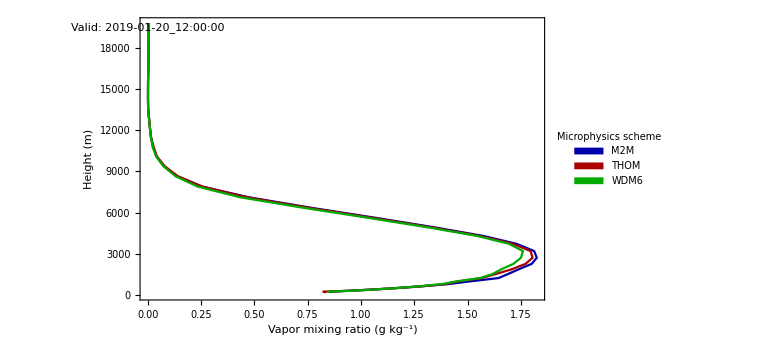

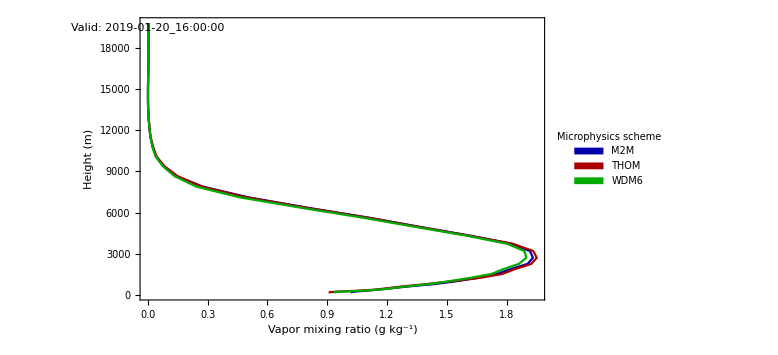

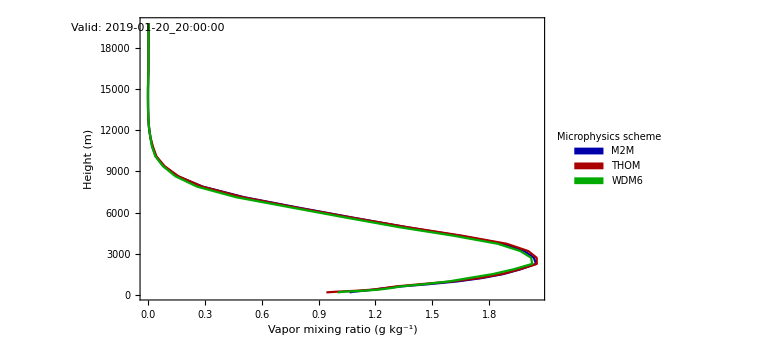

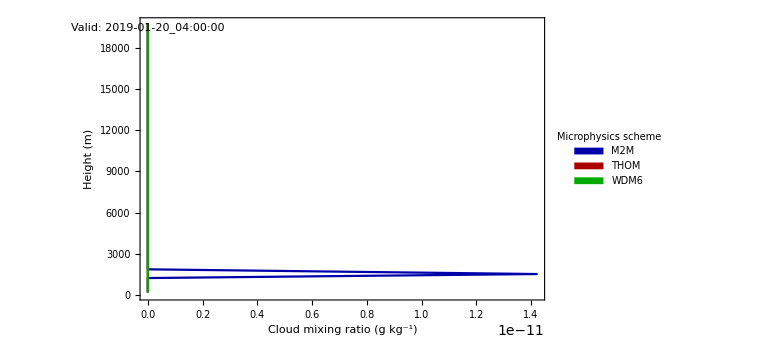

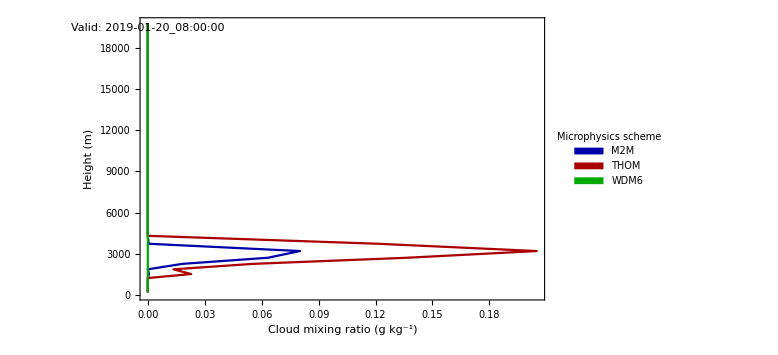

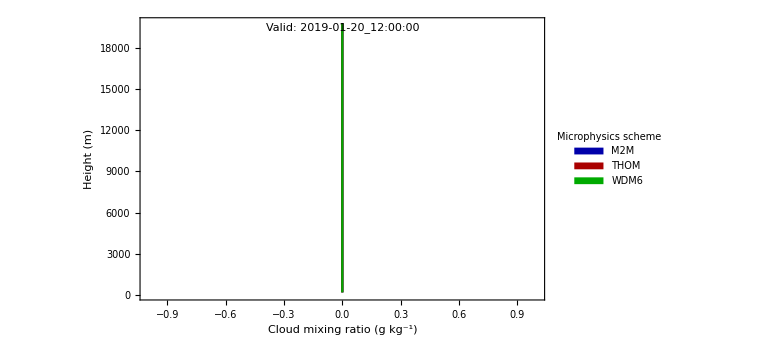

```mathematica
Do[Print[ListPlot[{listDataM2M⟦time⟧⟦type⟧,listDataTHOM⟦time⟧⟦type⟧,listDataWDM6⟦time⟧⟦type⟧},Frame->True,FrameLabel->{listTypes⟦type⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,All},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset[listTimes⟦time-1⟧,{Max[hydrometeorTHOM⟦time⟧⟦type⟧],19500}]]],{type,1,6},{time,2,6}];
```

```mathematica
Manipulate[ListPlot[{listDataM2M⟦time⟧⟦type⟧,listDataTHOM⟦time⟧⟦type⟧,listDataWDM6⟦time⟧⟦type⟧},Frame->True,FrameLabel->{listTypes⟦type⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,All},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset[listTimes⟦time-1⟧,{Max[hydrometeor⟦type⟧⟦time⟧],19500}]],{type,1,6,1},{time,2,6,1}]
```

## All hydrometeor data mixing ratios

```mathematica
(*Note: mixing ratio is defined as g of X per kg of air*)
```

```mathematica
(*As I have it now, I can only get data for one time efficiently in NCL. I need to figure out an effective way to loop through many times to get data for snow mixing ratio. Right now I only have 14:00 UTC *)
```

```mathematica
listTypes ={"Vapor mixing ratio (g kg^-1)","Cloud mixing ratio (g kg^-1)","Rain mixing ratio (g kg^-1)","Ice mixing ratio (g kg^-1)","Graupel mixing ratio (g kg^-1)","Snow mixing ratio (g kg^-1)"};
listTimes={"Valid: 2019-01-20_04:00:00","Valid: 2019-01-20_08:00:00","Valid: 2019-01-20_12:00:00","Valid: 2019-01-20_16:00:00","Valid: 2019-01-20_20:00:00"};
```

```mathematica
seperatetimesTHOM=Partition[Flatten[Import["midd_hydrometeor_dataTHOMtimes1.txt","CSV"]],912];
```

```mathematica
seperatetimesTHOM=Partition[Flatten[Import["midd_hydrometeor_dataTHOMtimes1.txt","CSV"]],912];
hydrometeorTHOM=Table[Partition[seperatetimesTHOM⟦i⟧,38],{i,1,6}];
listDataTHOM=Table[Table[Transpose[{hydrometeorTHOM⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,24}];
```

Transpose::nmtx: The first two levels of {{0.921394,0.890352,0.862273,0.827567,0.800027,0.831168,1.02735,1.3316,1.51267,1.52744,1.54023,1.61606,1.66366,1.67564,1.66017,1.48785,«6»,0.0785859,0.0407861,0.0232899,0.0156497,0.0134012,0.00862525,0.001,0.001,0.001,0.001,0.00242115,0.00273953,0.00305528,0.00343078,0.00389611,0.0044196},heights} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},heights} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

```mathematica
seperatetimesWDM6=Partition[Flatten[Import["midd_hydrometeor_dataWDM6times1.txt","CSV"]],912];
hydrometeorWDM6=Table[Partition[seperatetimesWDM6⟦i⟧,38],{i,1,6}];
listDataWDM6=Table[Table[Transpose[{hydrometeorWDM6⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,24}];
```

```mathematica
seperatetimesM2M=Partition[Flatten[Import["midd_hydrometeor_dataM2Mtimes1.txt","CSV"]],912];
hydrometeorM2M=Table[Partition[seperatetimesM2M⟦i⟧,38],{i,1,6}];
listDataM2M=Table[Table[Transpose[{hydrometeorM2M⟦type⟧⟦time⟧,heights}],{type,1,6}],{time,1,24}];
```

```mathematica
(*Do[Print[ListPlot[{listDataM2M⟦time⟧⟦type⟧,listDataTHOM⟦time⟧⟦type⟧,listDataWDM6⟦time⟧⟦type⟧},Frame->True,FrameLabel->{listTypes⟦type⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,All},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] , Epilog->Inset[listTimes⟦2⟧,{Max[hydrometeorTHOM⟦type⟧⟦time⟧],19500}]]],{type,1,6},{time,2,24}];*)
```

```mathematica
Manipulate[ListPlot[{listDataM2M⟦time⟧⟦type⟧,listDataTHOM⟦time⟧⟦type⟧,listDataWDM6⟦time⟧⟦type⟧},Frame->True,FrameLabel->{listTypes⟦type⟧, "Height (m)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,All},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] (*, Epilog->Inset[listTimes⟦2⟧,{Max[hydrometeor⟦type⟧⟦time⟧],19500}]*)],{type,1,6,1},{time,2,24,1}]
```

```mathematica
seperatetimesTH=Partition[Flatten[Import["domain_snowmix_dataTHOMtimes.txt","CSV"]],15504];
```

```mathematica
Length[seperatetimesTH]
```

24

```mathematica
heightsnowmixTH =Table[Partition[seperatetimesTH⟦i⟧,38],{i,1,24}]
```

{{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},404,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},22,{1}}
 |  |  |  |

```mathematica
Table[Table[Mean[heightsnowmixTH⟦grid⟧⟦level⟧],{grid,1,408}],{level,1,38}]
```

Part::pkspec1: The expression gridpoint cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 3 of {{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},«47»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},«358»},«23»}⟦gridpoint⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

## Tempeatures

```mathematica
GODDT2midd=Partition[Flatten[Import["midd_T2_dataGODD.txt", "CSV"]],49];
meanGODDT2midd=Mean[GODDT2midd- 273.15]; (*Subtract 273.15 to convert to degrees celcius*)
GODDT2times = Transpose[{DateandTime, meanGODDT2midd}];
THOMT2midd=Partition[Flatten[Import["midd_T2_dataTHOM.txt", "CSV"]],49];
meanTHOMT2midd=Mean[THOMT2midd - 273.15];
THOMT2times = Transpose[{DateandTime, meanTHOMT2midd}];
WDM6T2midd=Partition[Flatten[Import["midd_T2_dataWDM6.txt", "CSV"]],49];
meanWDM6T2midd=Mean[WDM6T2midd- 273.15];
WDM6T2times = Transpose[{DateandTime, meanWDM6T2midd}];
M2MT2midd=Partition[Flatten[Import["midd_T2_dataM2M.txt", "CSV"]],49];
meanM2MT2midd=Mean[M2MT2midd- 273.15];
M2MT2times = Transpose[{DateandTime, meanM2MT2midd}];
MILLT2midd=Partition[Flatten[Import["midd_T2_dataMILL.txt", "CSV"]],49];
meanMILLT2midd=Mean[MILLT2midd- 273.15];
MILLT2times = Transpose[{DateandTime, meanMILLT2midd}];
```

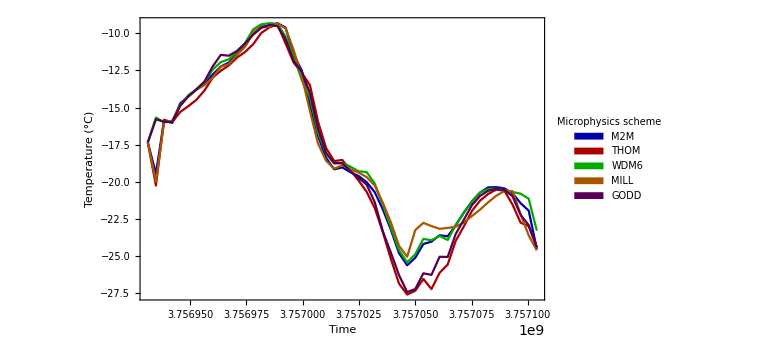

```mathematica
T2plot=DateListPlot[{meanM2MT2midd,meanTHOMT2midd,meanWDM6T2midd, meanMILLT2midd,meanGODDT2midd},{2019,1,20,00},Frame->True,FrameLabel->{"Time", "Temperature (°C)"},PlotStyle->{Darker[Blue],Darker[Red],Darker[Green],Darker[Orange],Darker[Purple]},LabelStyle->{Directive[Black,12],(FontFamily->"Times New Roman") }, Joined->True,GridLines->None
,PlotRange -> {{Automatic,Automatic},{0,Automatic}},ImageSize->Large,PlotLegends->SwatchLegend[{"M2M","THOM","WDM6", "MILL","GODD"}, LegendLabel ->"Microphysics scheme", LegendFunction->"Frame"] ]
```